```mathematica
(*OL*)
```

```mathematica
ol500c24h=metabgensteadystatehourset[24,0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{5232.46,Null}

```mathematica
ol500c24hkeep=keepallmetabmaintainsteadystate[ol500c24h[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{5143.18,Null}

```mathematica
ol500c24hmem=metabproteinmemfast[ol500c24hkeep];
```

```mathematica
ol500c24hkill=mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{1647.02,Null}

```mathematica
Histogram[ol500c24h[[1]][[4]]]
```

```mathematica
(*HP*)
```

```mathematica
{hpgen1,hpgen10,hpgen50,hpgen90,hpgen99}=Parallelize[{metabgensteadystatehourset[24,1,2.1,163,1,0,0,0,0,0,0,14,0.02],metabgensteadystatehourset[24,1,2.1,233,1,0,0,0,0,0,0,14,0.02],metabgensteadystatehourset[24,1,2.1,337,1,0,0,0,0,0,0,14,0.02],metabgensteadystatehourset[24,1,2.1,472,1,0,0,0,0,0,0,14,0.02],metabgensteadystatehourset[24,1,2.1,608,1,0,0,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{5522.13,Null}

```mathematica
{hpgen3000,hpgen6000}=Parallelize[{metabgensteadystatehourset[24,1,2.1,3000,1,0,0,0,0,0,0,14,0.02],metabgensteadystatehourset[24,1,2.1,6000,1,0,0,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{5472.46,Null}

```mathematica
{hmugen7000,hmugen14000}=Parallelize[{metabgensteadystatehourset[24,2,2.1,0,0,0,0,7000,1,0,0,14,0.02],metabgensteadystatehourset[24,2,2.1,0,0,0,0,14000,1,0,0,14,0.02]}];//AbsoluteTiming
```

{5336.73,Null}

```mathematica
{hpkeep3000,hpkeep6000,hmukeep7000,hmukeep14000}=Parallelize[{keepallmetabmaintainsteadystate[hpgen3000[[1]],1,2.1,3000,1,0,0,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hpgen6000[[1]],1,2.1,6000,1,0,0,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hmugen7000[[1]],2,2.1,0,0,0,0,7000,1,0,0,14,0.02],keepallmetabmaintainsteadystate[hmugen14000[[1]],2,2.1,0,0,0,0,14000,1,0,0,14,0.02]}];//AbsoluteTiming
```

{5393.22,Null}

```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\Zhang Lab\\Desktop\\source data\\ol500c24htest.mx"]
```

```mathematica
{hpkill3000,hpkill6000}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],1,2.1,3000,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,6000,1,0,0,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{5424.22,Null}

```mathematica
{}=Parallelize[{titeryieldproductivity[hpkill3000],titeryieldproductivity[hpkill6000]}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hplargecorrect.mx",{hpkill3000,hpkill6000,hptyp3000,hptyp6000}];
```

```mathematica
{hmukill7000,hmukill14000}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,7000,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,14000,1,0,0,14,0.02]}];//AbsoluteTiming
```

{5483.36,Null}

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hphmularge.mx",{hpgen3000,hpgen6000,hmugen7000,hmugen14000,hpkeep3000,hpkeep6000,hmukeep7000,hmukeep14000,hpkill3000,hpkill6000,hmukill7000,hmukill14000}];
```

```mathematica
{hpkeep1,hpkeep10,hpkeep50,hpkeep90,hpkeep99}=Parallelize[{keepallmetabmaintainsteadystate[hpgen1[[1]],1,2.1,163,1,0,0,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hpgen10[[1]],1,2.1,233,1,0,0,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hpgen50[[1]],1,2.1,337,1,0,0,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hpgen90[[1]],1,2.1,472,1,0,0,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hpgen99[[1]],1,2.1,608,1,0,0,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{5277.98,Null}

```mathematica
{hpmem1,hpmem10,hpmem50,hpmem90,hpmem99}=Parallelize[{metabproteinmemfast[hpkeep1],metabproteinmemfast[hpkeep10],metabproteinmemfast[hpkeep50],metabproteinmemfast[hpkeep90],metabproteinmemfast[hpkeep99]}];
```

```mathematica
(*KILL with OL, 24H*)
```

```mathematica
{hpkill1,hpkill10,hpkill50,hpkill90,hpkill99}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],1,2.1,163,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,233,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,337,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,472,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,608,1,0,0,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{2854.39,Null}

```mathematica
{hptyp1,hptyp10,hptyp50,hptyp90,hptyp99}=Parallelize[{titeryieldproductivity[hpkill1],titeryieldproductivity[hpkill10],titeryieldproductivity[hpkill50],titeryieldproductivity[hpkill90],titeryieldproductivity[hpkill99]}];
```

```mathematica
{hpkill400,hpkill500,hpkill600,hpkill700,hpkill900,hpkill1000,hpkill1100,hpkill1200,hpkill1300}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],1,2.1,400,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,500,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,600,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,700,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,900,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,1000,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,1100,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,1200,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],1,2.1,1300,1,0,0,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{3840.6,Null}

```mathematica
{hptyp400,hptyp500,hptyp600,hptyp700,hptyp900,hptyp1000,hptyp1100,hptyp1200,hptyp1300}=Parallelize[{titeryieldproductivity[hpkill400],titeryieldproductivity[hpkill500],titeryieldproductivity[hpkill600],titeryieldproductivity[hpkill700],titeryieldproductivity[hpkill900],titeryieldproductivity[hpkill1000],titeryieldproductivity[hpkill1100],titeryieldproductivity[hpkill1200],titeryieldproductivity[hpkill1300]}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hptyp.mx",{hptyp400,hptyp500,hptyp600,hptyp700,hptyp900,hptyp1000,hptyp1100,hptyp1200,hptyp1300,}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\ol500c24htest.mx",{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hp500c24hpercent.mx",{hpgen1,hpgen10,hpgen50,hpgen90,hpgen99,hpkeep1,hpkeep10,hpkeep50,hpkeep90,hpkeep99,hpmem1,hpmem10,hpmem50,hpmem90,hpmem99,hpkill1,hpkill10,hpkill50,hpkill90,hpkill99,hptyp1,hptyp10,hptyp50,hptyp90,hptyp99}];
```

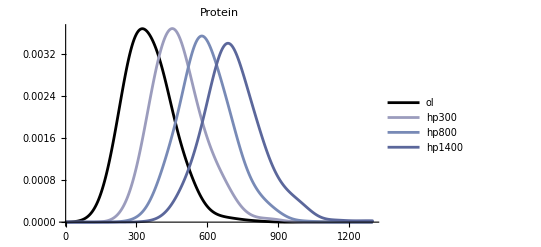

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hpgen300[[1]][[1]]/hpgen300[[1]][[6]],hpgen800[[1]][[1]]/hpgen800[[1]][[6]],hpgen1400[[1]][[1]]/hpgen1400[[1]][[6]]},50,PlotRange->{{0,1300},Automatic},PlotLegends->{"ol","hp300","hp800","hp1400"},PlotLabel->"Protein",PlotStyle->{Black,RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

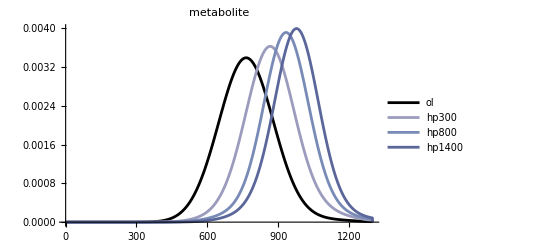

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hpgen300[[1]][[4]]/hpgen300[[1]][[6]],hpgen800[[1]][[4]]/hpgen800[[1]][[6]],hpgen1400[[1]][[4]]/hpgen1400[[1]][[6]]},80,PlotRange->{{0,1300},Automatic},PlotLegends->{"ol","hp300","hp800","hp1400"},PlotLabel->"metabolite",PlotStyle->{Black,RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

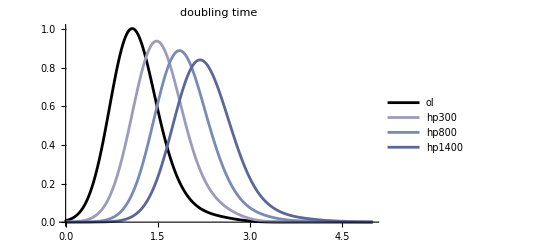

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hpgen300[[1]][[5]],Log[2]/hpgen800[[1]][[5]],Log[2]/hpgen1400[[1]][[5]]},0.3,PlotRange->{{0,5},Automatic},PlotLegends->{"ol","hp300","hp800","hp1400"},PlotLabel->"doubling time",PlotStyle->{Black,RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

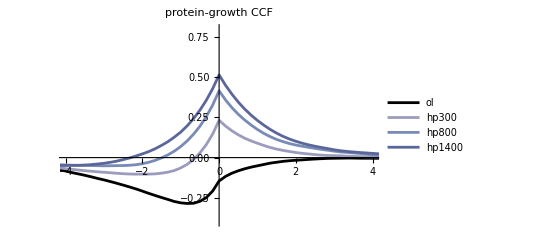

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hp300mem[[4]],hp800mem[[4]],hp1400mem[[4]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"ol","hp300","hp800","hp1400"},PlotLabel->"protein-growth CCF",PlotStyle->{Black,RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

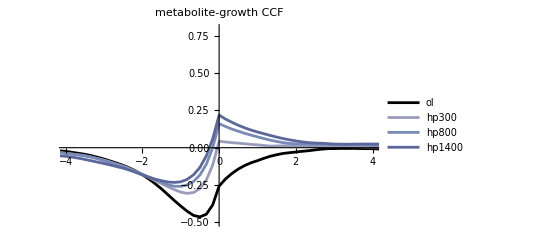

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hp300mem[[5]],hp800mem[[5]],hp1400mem[[5]]},PlotRange->{{-4,4},{-0.5,0.8}},PlotLegends->{"ol","hp300","hp800","hp1400"},PlotLabel->"metabolite-growth CCF",PlotStyle->{Black,RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

```mathematica
ListLinePlot[{oltyp[[1]],hp300typ[[1]],hp800typ[[1]],hp1400typ[[1]]},PlotLabel->"protein titer",PlotLegends->{"ol","hp300","hp800","hp1400"},PlotStyle->{Black,RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

-Graphics-

```mathematica
ListLinePlot[{oltyp[[3]],hp300typ[[3]],hp800typ[[3]],hp1400typ[[3]]},PlotLabel->"metabolite titer",PlotLegends->{"ol","hp300","hp800","hp1400"},PlotStyle->{Black,RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

-Graphics-

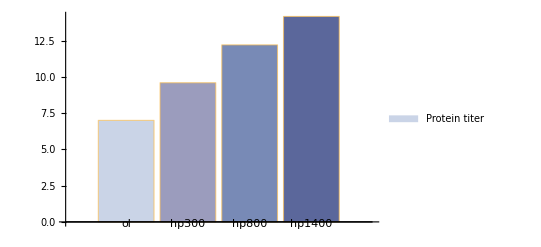

```mathematica
BarChart[{oltyp[[2]],hp300typ[[2]],hp800typ[[2]],hp1400typ[[2]]},ChartLegends->{"Protein titer"},ChartLabels->{"ol","hp300","hp800","hp1400"},ChartStyle->{RGBColor["#CAD4E7"],RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

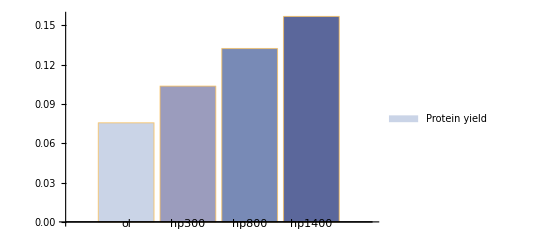

```mathematica
BarChart[{oltyp[[5]],hp300typ[[5]],hp800typ[[5]],hp1400typ[[5]]},ChartLegends->{"Protein yield"},ChartLabels->{"ol","hp300","hp800","hp1400"},ChartStyle->{RGBColor["#CAD4E7"],RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

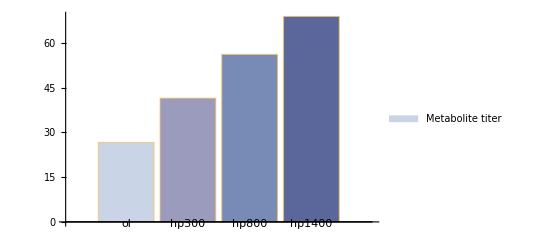

```mathematica
BarChart[{oltyp[[4]],hp300typ[[4]],hp800typ[[4]],hp1400typ[[4]]},ChartLegends->{"Metabolite titer"},ChartLabels->{"ol","hp300","hp800","hp1400"},ChartStyle->{RGBColor["#CAD4E7"],RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

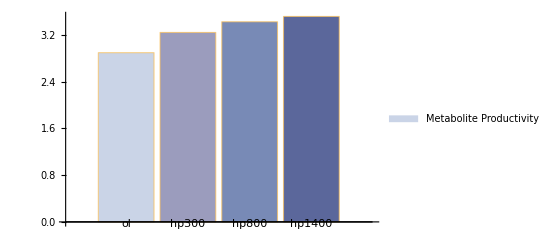

```mathematica
BarChart[{oltyp[[9]],hp300typ[[9]],hp800typ[[9]],hp1400typ[[9]]},ChartLegends->{"Metabolite Productivity"},ChartLabels->{"ol","hp300","hp800","hp1400"},ChartStyle->{RGBColor["#CAD4E7"],RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

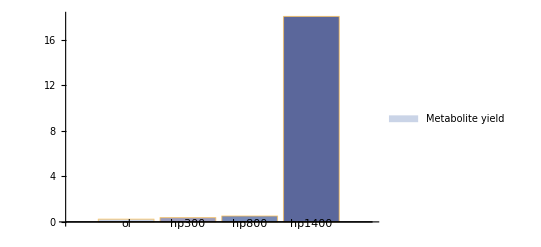

```mathematica
BarChart[{oltyp[[6]],hp300typ[[6]],hp800typ[[6]],hp1400typ[[6]]},ChartLegends->{"Metabolite yield"},ChartLabels->{"ol","hp300","hp800","hp1400"},ChartStyle->{RGBColor["#CAD4E7"],RGBColor["#9B9CBD"],RGBColor["#788AB6"],RGBColor["#5B679B"]}]
```

```mathematica
(*HYP*)
```

```mathematica
{hypgen1,hypgen10,hypgen50,hypgen90,hypgen99}=Parallelize[{metabgensteadystatehourset[24,0,2.1,0,0,2,1,0,0,0,0,14,0.02],metabgensteadystatehourset[24,0,2.1,0,0,4,1,0,0,0,0,14,0.02],metabgensteadystatehourset[24,0,2.1,0,0,7,1,0,0,0,0,14,0.02],metabgensteadystatehourset[24,0,2.1,0,0,10,1,0,0,0,0,14,0.02],metabgensteadystatehourset[24,0,2.1,0,0,14,1,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{5565.61,Null}

```mathematica
{hypkeep1,hypkeep10,hypkeep50,hypkeep90,hypkeep99}=Parallelize[{keepallmetabmaintainsteadystate[hypgen1[[1]],0,2.1,0,0,2,1,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hypgen10[[1]],0,2.1,0,0,4,1,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hypgen50[[1]],0,2.1,0,0,7,1,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hypgen90[[1]],0,2.1,0,0,10,1,0,0,0,0,14,0.02],keepallmetabmaintainsteadystate[hypgen99[[1]],0,2.1,0,0,14,1,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{5294.29,Null}

```mathematica
{hypmem1,hypmem10,hypmem50,hypmem90,hypmem99}=Parallelize[{metabproteinmemfast[hypkeep1],metabproteinmemfast[hypkeep10],metabproteinmemfast[hypkeep50],metabproteinmemfast[hypkeep90],metabproteinmemfast[hypkeep99]}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hyp500c24hpercent.mx",{hypgen1,hypgen10,hypgen50,hypgen90,hypgen99,hypkeep1,hypkeep10,hypkeep50,hypkeep90,hypkeep99,hypmem1,hypmem10,hypmem50,hypmem90,hypmem99,hypkill1,hypkill10,hypkill50,hypkill90,hypkill99,hyptyp1,hyptyp10,hyptyp50,hyptyp90,hyptyp99}];
```

```mathematica
{hypkill1,hypkill10,hypkill50,hypkill90,hypkill99}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,2,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,4,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,7,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,10,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,14,1,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{1719.26,Null}

```mathematica
{hyptyp1,hyptyp10,hyptyp50,hyptyp90,hyptyp99}=Parallelize[{titeryieldproductivity[hypkill1],titeryieldproductivity[hypkill10],titeryieldproductivity[hypkill50],titeryieldproductivity[hypkill90],titeryieldproductivity[hypkill99]}];
```

```mathematica
{hypkill2,hypkill3,hypkill4,hypkill5,hypkill6,hypkill7,hypkill9,hypkill10,hypkill11,hypkill12,hypkill13,hypkill14,hypkill15}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,2,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,3,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,4,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,5,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,6,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,7,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,9,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,10,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,11,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,12,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,13,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,14,1,0,0,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,15,1,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{1908.63,Null}

```mathematica
{hyptyp2,hyptyp3,hyptyp4,hyptyp5,hyptyp6,hyptyp7,hyptyp9,hyptyp10,hyptyp11,hyptyp12,hyptyp13,hyptyp14,hyptyp15}=Parallelize[{titeryieldproductivity[hypkill2],titeryieldproductivity[hypkill3],titeryieldproductivity[hypkill4],titeryieldproductivity[hypkill5],titeryieldproductivity[hypkill6],titeryieldproductivity[hypkill7],titeryieldproductivity[hypkill9],titeryieldproductivity[hypkill10],titeryieldproductivity[hypkill11],titeryieldproductivity[hypkill12],titeryieldproductivity[hypkill13],titeryieldproductivity[hypkill14],titeryieldproductivity[hypkill15]}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hyptyp.mx",{hyptyp2,hyptyp3,hyptyp4,hyptyp5,hyptyp6,hyptyp7,hyptyp9,hyptyp10,hyptyp11,hyptyp12,hyptyp13,hyptyp14,hyptyp15}];
```

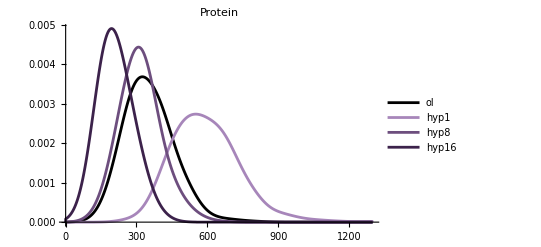

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hypgen1[[1]][[1]]/hypgen1[[1]][[6]],hypgen8[[1]][[1]]/hypgen8[[1]][[6]],hypgen16[[1]][[1]]/hypgen16[[1]][[6]]},50,PlotRange->{{0,1300},Automatic},PlotLegends->{"ol","hyp1","hyp8","hyp16"},PlotLabel->"Protein",PlotStyle->{Black,RGBColor["#A786BA"],RGBColor["#6D4E7E"],RGBColor["#3C224B"]}]
```

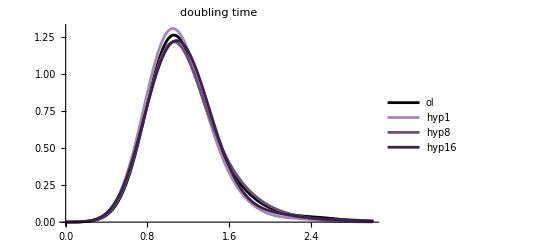

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hypgen1[[1]][[5]],Log[2]/hypgen8[[1]][[5]],Log[2]/hypgen16[[1]][[5]]},0.2,PlotRange->{{0,3},Automatic},PlotLegends->{"ol","hyp1","hyp8","hyp16"},PlotLabel->"doubling time",PlotStyle->{Black,RGBColor["#A786BA"],RGBColor["#6D4E7E"],RGBColor["#3C224B"]}]
```

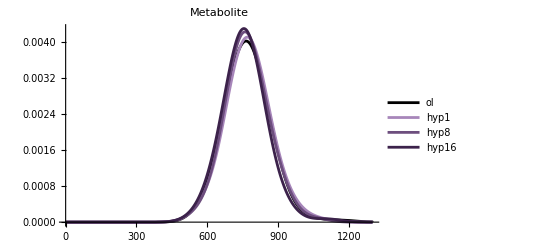

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hypgen1[[1]][[4]]/hypgen1[[1]][[6]],hypgen8[[1]][[4]]/hypgen8[[1]][[6]],hypgen16[[1]][[4]]/hypgen16[[1]][[6]]},50,PlotRange->{{0,1300},Automatic},PlotLegends->{"ol","hyp1","hyp8","hyp16"},PlotLabel->"Metabolite",PlotStyle->{Black,RGBColor["#A786BA"],RGBColor["#6D4E7E"],RGBColor["#3C224B"]}]
```

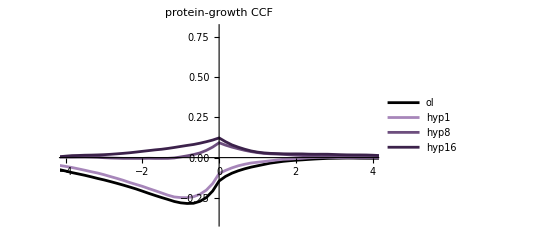

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hyp1mem[[4]],hyp8mem[[4]],hyp16mem[[4]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"ol","hyp1","hyp8","hyp16"},PlotLabel->"protein-growth CCF",PlotStyle->{Black,RGBColor["#A786BA"],RGBColor["#6D4E7E"],RGBColor["#3C224B"]}]
```

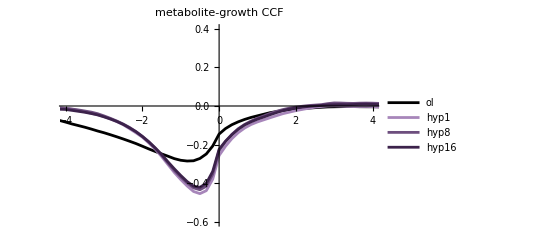

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hyp1mem[[5]],hyp8mem[[5]],hyp16mem[[5]]},PlotRange->{{-4,4},{-0.6,0.4}},PlotLegends->{"ol","hyp1","hyp8","hyp16"},PlotLabel->"metabolite-growth CCF",PlotStyle->{Black,RGBColor["#A786BA"],RGBColor["#6D4E7E"],RGBColor["#3C224B"]}]
```

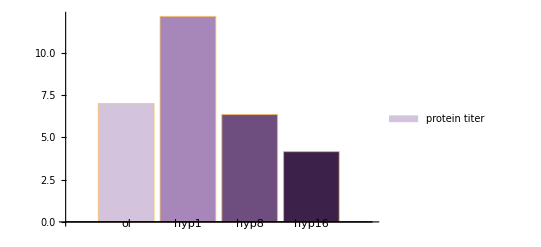

```mathematica
BarChart[{oltyp[[2]],hyp1typ[[2]],hyp8typ[[2]],hyp16typ[[2]]},ChartLegends->{"protein titer"},ChartLabels->{"ol","hyp1","hyp8","hyp16"},ChartStyle->{RGBColor["#D3C3DD"],RGBColor["#A786BA"],RGBColor["#6D4E7E"],RGBColor["#3C224B"]}]
```

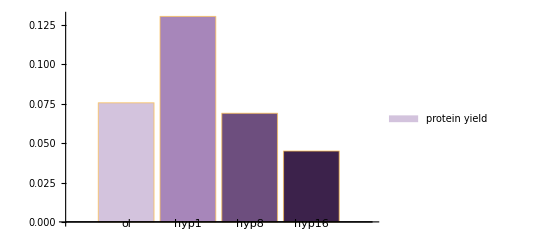

```mathematica
BarChart[{oltyp[[5]],hyp1typ[[5]],hyp8typ[[5]],hyp16typ[[5]]},ChartLegends->{"protein yield"},ChartLabels->{"ol","hyp1","hyp8","hyp16"},ChartStyle->{RGBColor["#D3C3DD"],RGBColor["#A786BA"],RGBColor["#6D4E7E"],RGBColor["#3C224B"]}]
```

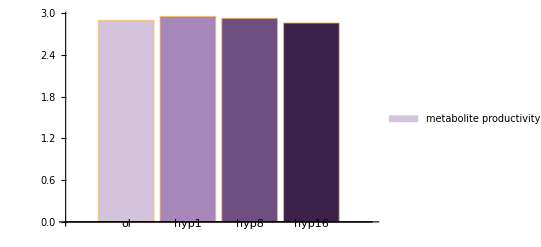

```mathematica
BarChart[{oltyp[[9]],hyp1typ[[9]],hyp8typ[[9]],hyp16typ[[9]]},ChartLegends->{"metabolite productivity"},ChartLabels->{"ol","hyp1","hyp8","hyp16"},ChartStyle->{RGBColor["#D3C3DD"],RGBColor["#A786BA"],RGBColor["#6D4E7E"],RGBColor["#3C224B"]}]
```

```mathematica
(*HMU*)
```

## (*small hmu values*)

```mathematica
{hmugen1,hmugen10,hmugen50,hmugen90,hmugen99}=Parallelize[{metabgensteadystatehourset[24,2,2.1,0,0,0,0,563,1,0,0,14,0.02],metabgensteadystatehourset[24,2,2.1,0,0,0,0,663,1,0,0,14,0.02],metabgensteadystatehourset[24,2,2.1,0,0,0,0,767,1,0,0,14,0.02],metabgensteadystatehourset[24,2,2.1,0,0,0,0,880,1,0,0,14,0.02],metabgensteadystatehourset[24,2,2.1,0,0,0,0,1030,1,0,0,14,0.02]}];//AbsoluteTiming
```

{5527.3,Null}

```mathematica
{hmukeep1,hmukeep10,hmukeep50,hmukeep90,hmukeep99}=Parallelize[{keepallmetabmaintainsteadystate[hmugen1[[1]],2,2.1,0,0,0,0,563,1,0,0,14,0.02],keepallmetabmaintainsteadystate[hmugen10[[1]],2,2.1,0,0,0,0,663,1,0,0,14,0.02],keepallmetabmaintainsteadystate[hmugen50[[1]],2,2.1,0,0,0,0,767,1,0,0,14,0.02],keepallmetabmaintainsteadystate[hmugen90[[1]],2,2.1,0,0,0,0,880,1,0,0,14,0.02],keepallmetabmaintainsteadystate[hmugen99[[1]],2,2.1,0,0,0,0,1030,1,0,0,14,0.02]}];//AbsoluteTiming
```

{5288.93,Null}

```mathematica
hmu1400keep=keepallmetabmaintainsteadystate[hmu1400gen[[1]],2,2.1,0,0,0,0,1400,1,0,0,14,0.02];
```

```mathematica
{hmumem1,hmumem10,hmumem50,hmumem90,hmumem99}=Parallelize[{metabproteinmemfast[hmukeep1],metabproteinmemfast[hmukeep10],metabproteinmemfast[hmukeep50],metabproteinmemfast[hmukeep90],metabproteinmemfast[hmukeep99]}];
```

```mathematica
hmu1400mem=metabproteinmemfast[hmu1400keep];
```

```mathematica
{hmukill1,hmukill10,hmukill50,hmukill90,hmukill99}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,563,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,663,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,767,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,880,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,1030,1,0,0,14,0.02]}];//AbsoluteTiming
```

{2834.73,Null}

```mathematica
{hmukill500,hmukill600,hmukill700,hmukill900,hmukill1000,hmukill1100,hmukill1200,hmukill1300}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,500,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,600,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,700,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,900,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,1000,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,1100,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,1200,1,0,0,14,0.02],mxcontkilling[24,ol500c24h[[1]],2,2.1,0,0,0,0,1300,1,0,0,14,0.02]}];//AbsoluteTiming
```

{3234.84,Null}

```mathematica
{hmutyp500,hmutyp600,hmutyp700,hmutyp900,hmutyp1000,hmutyp1100,hmutyp1200,hmutyp1300}=Parallelize[{titeryieldproductivity[hmukill500],titeryieldproductivity[hmukill600],titeryieldproductivity[hmukill700],titeryieldproductivity[hmukill900],titeryieldproductivity[hmukill1000],titeryieldproductivity[hmukill1100],titeryieldproductivity[hmukill1200],titeryieldproductivity[hmukill1300]}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hmu500c24hpercent.mx",{hmugen1,hmugen10,hmugen50,hmugen90,hmugen99,hmukeep1,hmukeep10,hmukeep50,hmukeep90,hmukeep99,hmumem1,hmumem10,hmumem50,hmumem90,hmumem99,hmukill1,hmukill10,hmukill50,hmukill90,hmukill99,hmutyp1,hmutyp10,hmutyp50,hmutyp90,hmutyp99}];
```

```mathematica
{hmutyp1,hmutyp10,hmutyp50,hmutyp90,hmutyp99}=Parallelize[{titeryieldproductivity[hmukill1],titeryieldproductivity[hmukill10],titeryieldproductivity[hmukill50],titeryieldproductivity[hmukill90],titeryieldproductivity[hmukill99]}];
```

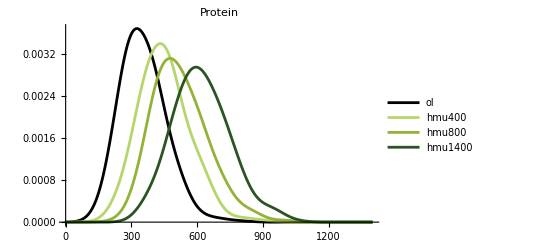

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hmu400gen[[1]][[1]]/hmu400gen[[1]][[6]],hmu800gen[[1]][[1]]/hmu800gen[[1]][[6]],hmu1400gen[[1]][[1]]/hmu1400gen[[1]][[6]]},50,PlotRange->{{0,1400},Automatic},PlotLegends->{"ol","hmu400","hmu800","hmu1400"},PlotLabel->"Protein",PlotStyle->{Black,RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

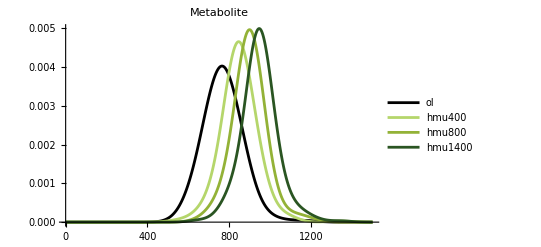

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hmu400gen[[1]][[4]]/hmu400gen[[1]][[6]],hmu800gen[[1]][[4]]/hmu800gen[[1]][[6]],hmu1400gen[[1]][[4]]/hmu1400gen[[1]][[6]]},50,PlotRange->{{0,1500},Automatic},PlotLegends->{"ol","hmu400","hmu800","hmu1400"},PlotLabel->"Metabolite",PlotStyle->{Black,RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

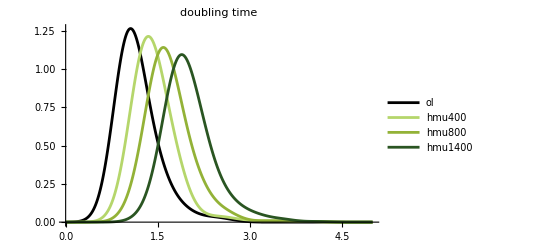

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hmu400gen[[1]][[5]],Log[2]/hmu800gen[[1]][[5]],Log[2]/hmu1400gen[[1]][[5]]},0.2,PlotRange->{{0,5},Automatic},PlotLegends->{"ol","hmu400","hmu800","hmu1400"},PlotLabel->"doubling time",PlotStyle->{Black,RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

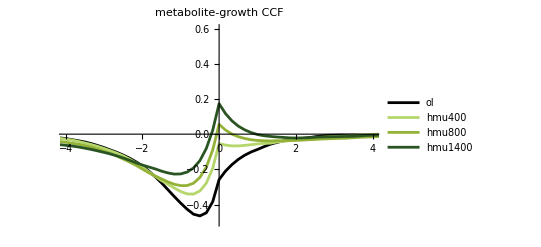

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hmu400mem[[5]],hmu800mem[[5]],hmu1400mem[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"ol","hmu400","hmu800","hmu1400"},PlotLabel->"metabolite-growth CCF",PlotStyle->{Black,RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

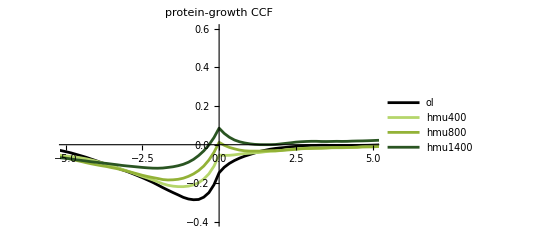

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hmu400mem[[4]],hmu800mem[[4]],hmu1400mem[[4]]},PlotRange->{{-5,5},{-0.4,0.6}},PlotLegends->{"ol","hmu400","hmu800","hmu1400"},PlotLabel->"protein-growth CCF",PlotStyle->{Black,RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

```mathematica
ListLinePlot[{oltyp[[1]],hmu400typ[[1]],hmu800typ[[1]],hmu1400typ[[1]]},PlotLabel->"protein titer",PlotLegends->{"ol","hmu400","hmu800","hmu1400"},PlotStyle->{Black,RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

-Graphics-

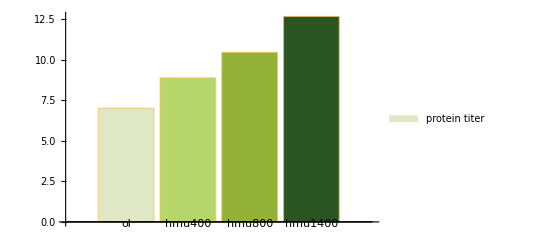

```mathematica
BarChart[{oltyp[[2]],hmu400typ[[2]],hmu800typ[[2]],hmu1400typ[[2]]},ChartLegends->{"protein titer"},ChartLabels->{"ol","hmu400","hmu800","hmu1400"},ChartStyle->{RGBColor["#DFE7C4"],RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

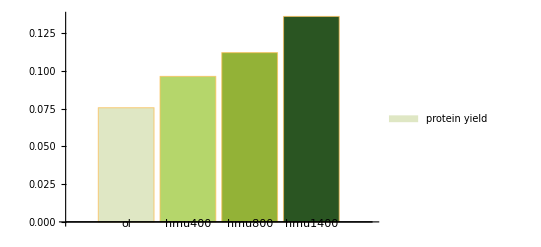

```mathematica
BarChart[{oltyp[[5]],hmu400typ[[5]],hmu800typ[[5]],hmu1400typ[[5]]},ChartLegends->{"protein yield"},ChartLabels->{"ol","hmu400","hmu800","hmu1400"},ChartStyle->{RGBColor["#DFE7C4"],RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

```mathematica
ListLinePlot[{oltyp[[3]],hmu400typ[[3]],hmu800typ[[3]],hmu1400typ[[3]]},PlotLabel->"metabolite titer",PlotLegends->{"ol","hmu400","hmu800","hmu1400"},PlotStyle->{Black,RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

-Graphics-

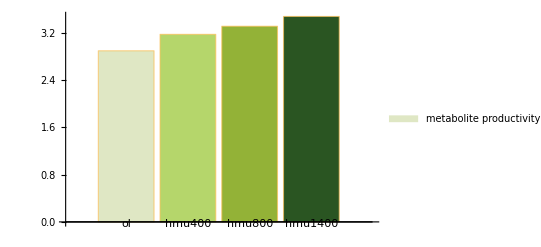

```mathematica
BarChart[{oltyp[[9]],hmu400typ[[9]],hmu800typ[[9]],hmu1400typ[[9]]},ChartLegends->{"metabolite productivity"},ChartLabels->{"ol","hmu400","hmu800","hmu1400"},ChartStyle->{RGBColor["#DFE7C4"],RGBColor["#B5D66B"],RGBColor["#93B237"],RGBColor["#2A5522"]}]
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hmu500c24htest.mx",{hmu400gen,hmu800gen,hmu1400gen,hmu400keep,hmu800keep,hmu1400keep,hmu400kill,hmu800kill,hmu1400kill,hmu400mem,hmu800mem,hmu1400mem,hmu400typ,hmu800typ,hmu1400typ}];
```

```mathematica
(*HMP*)
```

## (*small hmp values*)

```mathematica
{hmpgen1,hmpgen10,hmpgen50,hmpgen90,hmpgen99}=Parallelize[{metabgensteadystatehourset[24,0,2.1,0,0,0,0,0,0,563,1,14,0.02],metabgensteadystatehourset[24,0,2.1,0,0,0,0,0,0,663,1,14,0.02],metabgensteadystatehourset[24,0,2.1,0,0,0,0,0,0,767,1,14,0.02],metabgensteadystatehourset[24,0,2.1,0,0,0,0,0,0,880,1,14,0.02],metabgensteadystatehourset[24,0,2.1,0,0,0,0,0,0,1030,1,14,0.02]}];//AbsoluteTiming
```

{5486.38,Null}

```mathematica
{hmpkeep1,hmpkeep10,hmpkeep50,hmpkeep90,hmpkeep99}=Parallelize[{keepallmetabmaintainsteadystate[hmpgen1[[1]],0,2.1,0,0,0,0,0,0,563,1,14,0.02],keepallmetabmaintainsteadystate[hmpgen10[[1]],0,2.1,0,0,0,0,0,0,663,1,14,0.02],keepallmetabmaintainsteadystate[hmpgen50[[1]],0,2.1,0,0,0,0,0,0,767,1,14,0.02],keepallmetabmaintainsteadystate[hmpgen90[[1]],0,2.1,0,0,0,0,0,0,880,1,14,0.02],keepallmetabmaintainsteadystate[hmpgen99[[1]],0,2.1,0,0,0,0,0,0,1030,1,14,0.02]}];//AbsoluteTiming
```

{5286.54,Null}

```mathematica
{hmpmem1,hmpmem10,hmpmem50,hmpmem90,hmpmem99}=Parallelize[{metabproteinmemfast[hmpkeep1],metabproteinmemfast[hmpkeep10],metabproteinmemfast[hmpkeep50],metabproteinmemfast[hmpkeep90],metabproteinmemfast[hmpkeep99]}];
```

```mathematica
{hmp400kill,hmp800kill,hmp1400kill}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,400,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,800,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,1400,1,14,0.02]}];//AbsoluteTiming
```

{1734.94,Null}

```mathematica
{hmp400typ,hmp800typ,hmp1400typ}=Parallelize[{titeryieldproductivity[hmp400kill],titeryieldproductivity[hmp800kill],titeryieldproductivity[hmp1400kill]}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hmp500c24htest.mx",{hmp400gen,hmp800gen,hmp1400gen,hmp400keep,hmp800keep,hmp1400keep,hmp400kill,hmp800kill,hmp1400kill,hmp400mem,hmp800mem,hmp1200mem,hmp400typ,hmp800typ,hmp1400typ}];
```

```mathematica
{hmpkill500,hmpkill600,hmpkill700,hmpkill900,hmpkill1000,hmpkill1100,hmpkill1200,hmpkill1300}=Parallelize[{mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,500,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,600,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,700,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,900,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,1000,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,1100,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,1200,1,14,0.02],mxcontkilling[24,ol500c24h[[1]],0,2.1,0,0,0,0,0,0,1300,1,14,0.02]}];//AbsoluteTiming
```

{1810.23,Null}

```mathematica
{hmptyp500,hmptyp600,hmptyp700,hmptyp900,hmptyp1000,hmptyp1100,hmptyp1200,hmptyp1300}=Parallelize[{titeryieldproductivity[hmpkill500],titeryieldproductivity[hmpkill600],titeryieldproductivity[hmpkill700],titeryieldproductivity[hmpkill900],titeryieldproductivity[hmpkill1000],titeryieldproductivity[hmpkill1100],titeryieldproductivity[hmpkill1200],titeryieldproductivity[hmpkill1300]}];
```

```mathematica
Export["C:\\Users\\Zhang Lab\\Desktop\\source data\\hmptyp.mx",{hmptyp500,hmptyp600,hmptyp700,hmptyp900,hmptyp1000,hmptyp1100,hmptyp1200,hmptyp1300}];
```

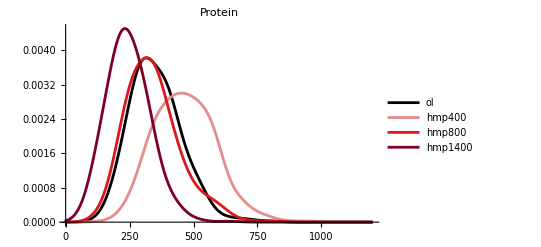

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hmp400gen[[1]][[1]]/hmp400gen[[1]][[6]],hmp800gen[[1]][[1]]/hmp800gen[[1]][[6]],hmp1400gen[[1]][[1]]/hmp1400gen[[1]][[6]]},40,PlotRange->{{0,1200},Automatic},PlotLegends->{"ol","hmp400","hmp800","hmp1400"},PlotLabel->"Protein",PlotStyle->{Black,RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

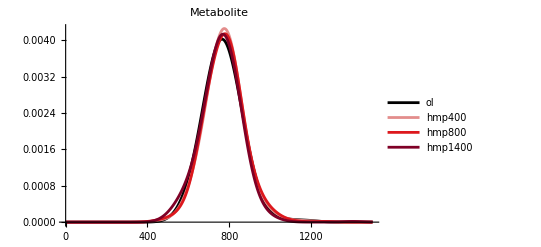

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hmp400gen[[1]][[4]]/hmp400gen[[1]][[6]],hmp800gen[[1]][[4]]/hmp800gen[[1]][[6]],hmp1400gen[[1]][[4]]/hmp1400gen[[1]][[6]]},50,PlotRange->{{0,1500},Automatic},PlotLegends->{"ol","hmp400","hmp800","hmp1400"},PlotLabel->"Metabolite",PlotStyle->{Black,RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

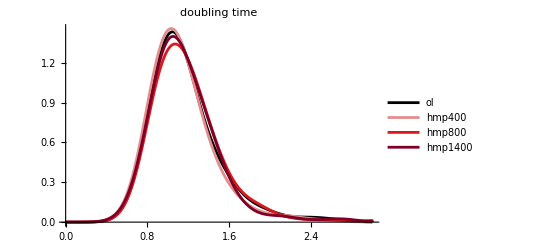

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hmp400gen[[1]][[5]],Log[2]/hmp800gen[[1]][[5]],Log[2]/hmp1400gen[[1]][[5]]},0.15,PlotRange->{{0,3},Automatic},PlotLegends->{"ol","hmp400","hmp800","hmp1400"},PlotLabel->"doubling time",PlotStyle->{Black,RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

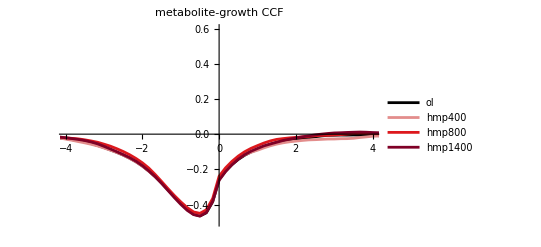

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hmp400mem[[5]],hmp800mem[[5]],hmp1200mem[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"ol","hmp400","hmp800","hmp1400"},PlotLabel->"metabolite-growth CCF",PlotStyle->{Black,RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

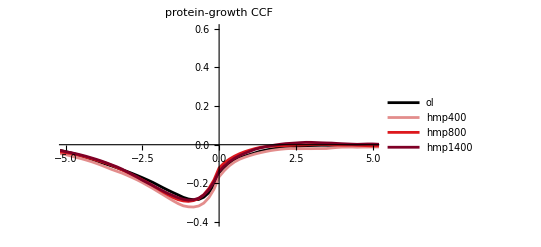

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hmp400mem[[4]],hmp800mem[[4]],hmp1200mem[[4]]},PlotRange->{{-5,5},{-0.4,0.6}},PlotLegends->{"ol","hmp400","hmp800","hmp1400"},PlotLabel->"protein-growth CCF",PlotStyle->{Black,RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

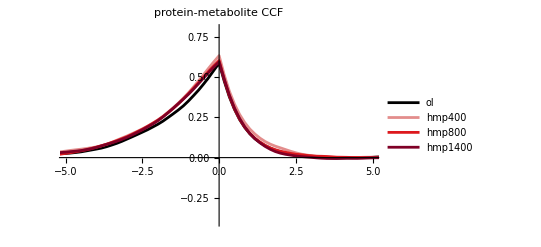

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hmp400mem[[6]],hmp800mem[[6]],hmp1200mem[[6]]},PlotRange->{{-5,5},{-0.4,0.8}},PlotLegends->{"ol","hmp400","hmp800","hmp1400"},PlotLabel->"protein-metabolite CCF",PlotStyle->{Black,RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

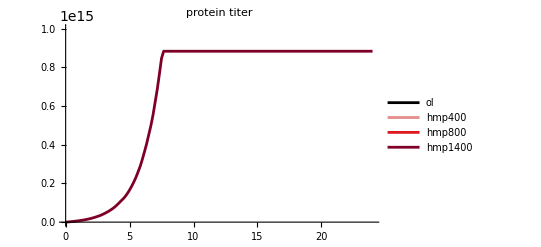

```mathematica
ListLinePlot[{oltyp[[1]],hmp400typ[[1]],hmp800typ[[1]],hmp1400typ[[1]]},PlotLabel->"protein titer",PlotLegends->{"ol","hmp400","hmp800","hmp1400"},PlotStyle->{Black,RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

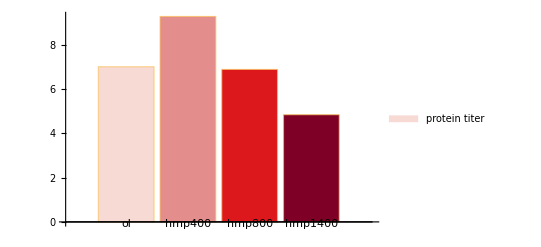

```mathematica
BarChart[{oltyp[[2]],hmp400typ[[2]],hmp800typ[[2]],hmp1400typ[[2]]},ChartLegends->{"protein titer"},ChartLabels->{"ol","hmp400","hmp800","hmp1400"},ChartStyle->{RGBColor["#F8DAD5"],RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

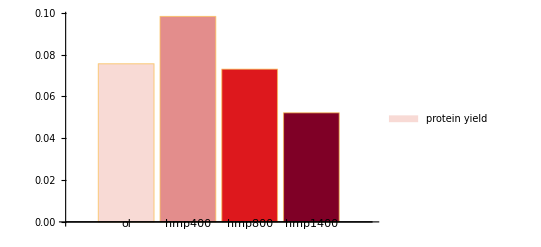

```mathematica
BarChart[{oltyp[[5]],hmp400typ[[5]],hmp800typ[[5]],hmp1400typ[[5]]},ChartLegends->{"protein yield"},ChartLabels->{"ol","hmp400","hmp800","hmp1400"},ChartStyle->{RGBColor["#F8DAD5"],RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

```mathematica
ListLinePlot[{oltyp[[3]],hmp400typ[[3]],hmp800typ[[3]],hmp1400typ[[3]]},PlotLabel->"metabolite titer",PlotLegends->{"ol","hmp400","hmp800","hmp1400"},PlotStyle->{RGBColor["#F8DAD5"],RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```

-Graphics-

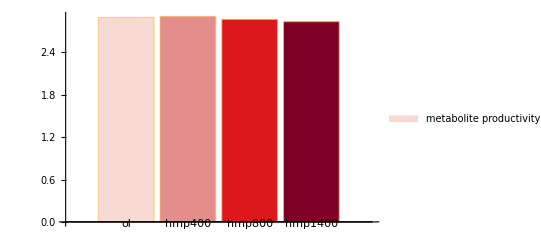

```mathematica
BarChart[{oltyp[[9]],hmp400typ[[9]],hmp800typ[[9]],hmp1400typ[[9]]},ChartLegends->{"metabolite productivity"},ChartLabels->{"ol","hmp400","hmp800","hmp1400"},ChartStyle->{RGBColor["#F8DAD5"],RGBColor["#E38D8C"],RGBColor["#DD181D"],RGBColor["#7F0026"]}]
```